```mathematica
Lecture 12 Mathematica Functions and Functional Programming
```

## Assignment: Immediate (=) vs Delayed (:=)

```mathematica
t=Now
```

```mathematica
t
```

```mathematica
t
```

```mathematica
t:= Now (*Delayed Assignment, do not assign now and recomputed each time when needed*)
```

```mathematica
t
```

```mathematica
t
```

```mathematica
x = RandomInteger[5]
```

```mathematica
Table[x,5]
```

```mathematica
y := RandomInteger[5]
```

```mathematica
Table[y,5]
```

```mathematica
Table[RandomInteger[5],5] (*equivalent way*)
```

## Function Definitions

General form to define Mathematica functions
Key issues are  _ (officially called Blank in Mathematica) in LHS and the delayed assignment :=

```mathematica
f[x_,y_]:= x+y (*note the _ in LHS, and the :=*)
```

```mathematica
?f
```

```mathematica
f[1,2]
```

```mathematica
f[a,1]
```

```mathematica
f[a,b]
```

```mathematica
f1[x,y]:=x+y (*a wrong definition*)
f1[x,y]
f1[1,2]
```

x+y

f1[1,2]

```mathematica
x = 1;y=2;
f2[x_,y_] = x+y(*another imperfect definition*)
f2[3,4]
Clear[x,y]
```

3

3

```mathematica
g[x_]:=Sin[x]/(1+x^2)
```

```mathematica
g'[b]
```

```mathematica
D[g[b],b] (*equivalent way*)
```

```mathematica
Plot[g[x],{x,0,Pi}]
```

```mathematica
h[x_]:=g'[x] (*define the derivative function*)
```

```mathematica
h[x]
```

```mathematica
Plot[h[x],{x,0,Pi}]
```

Recursive Functions

```mathematica
Ffib[1] =0;
Ffib[2] = 1;
Ffib[k_]:=Ffib[k-1]+Ffib[k-2] (*define fibonacci sequence in recursive way*)
```

```mathematica
Ffib[8]
```

```mathematica
fib = Table[Ffib[n],{n,1,20}]
```

Exercise: use recursive function method to generate list of length 10 as {1,x, 1+x, 1+x+x^2/2!, ...,}, whose n-th term is  ∑_(k=1)^n x^(k-1)/((k-1)!).

Conditional

Use /; (pattern constraints) at RHS to specify the domain of definition

```mathematica
?/;
```

```mathematica
Clear[f]
f[x_,y_]:=x-y /; x>y
```

```mathematica
f[2,1]
```

```mathematica
f[1,2]
```

```mathematica
Clear[f]
f[x_]:=-x /; x<0
f[x_]:=0 /; x==0
f[x_] := x/;x>0 (*can also use x>=0, i.e. input >followed by =*)
```

```mathematica
Plot[f[x],{x,-5,5}]
```

Exercise: Redefine the function with Piecewise command in Mathematica

```mathematica
Pure Functions
```

The command Function and equivalently with pound symbol # and ampersand & symbol can be used to define pure functions (similar to anonymous functions in Matlab). In functional programming, pure function means the function will always produce the same output given the same input, and won’t change the state of environment (no side effect).

```mathematica
?Function
```

```mathematica
Function[z,z^2][2]
```

```mathematica
(#^2&)[6]
```

```mathematica
squared1 = Function[z,z^2];
squared1[6]
```

```mathematica
squared2 = #^2&;
squared2[6]
```

```mathematica
g=(#1+#2)& (*first and second input*)
g[4,5]
```

## Function Calling and Functional Programming

In computer science, functional programming is an important programming paradigm that stresses writing programs with applying and composing functions (in contrast with procedural programming which focuses on variables, statements and flow controls). Mathematica has good support for the functional programming paradigm.

### Calling Function with @ and //

```mathematica
Clear[f,x]
f@x
```

f[x]

```mathematica
x//f
```

f[x]

```mathematica
Table[f[x],{x,1,10}]//FullForm
```

List[f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]]

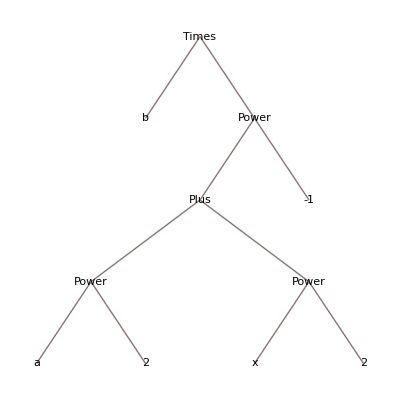

```mathematica
b/(x^2+a^2) //TreeForm
```

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

### Map (/@) and Apply (@@)

One important feature in functional programming is that functions are first-class citizens -- they serve as the arguments of other functions just as other data type can. In Mathematica, the important functions (higher-order functions) to “manipulate” or “operate” other functions (accept other functions as input) include Map and Apply. They are borrowed from ideas like “operators” “functionals” in pure math/theoretical physics.

```mathematica
Clear[f]
myList = Range[10];
Map[f,myList] (*equivalent to Table[f[x],{x,1,10}]*)
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
f/@myList
```

```mathematica
{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}
```

```mathematica
Apply[f,myList]
```

f[1,2,3,4,5,6,7,8,9,10]

```mathematica
f@@myList
```

f[1,2,3,4,5,6,7,8,9,10]

```mathematica
f[myList] (*this is neither map nor apply*)
```

f[{1,2,3,4,5,6,7,8,9,10}]

```mathematica
Head /@ {Pi,22/7,3}
```

{Symbol,Rational,Integer}

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

```mathematica
Plus @@{a,b,c}
```

a+b+c

Exercise: 
1. Use apply to get (abc)^(1/3). In general, define the function gmean to get the geometric mean of any list. 
2. Analyze and understand the following command

```mathematica
Map[Power @@ # &, {{a,b},{c,d}}]
```

{a^b,c^d}

```mathematica
Times @@ (Power @@ # & /@ {{a,b},{c,d}})
```

a^b c^d

```mathematica
?Listable
```

Remark : Map is relevant to the Listable attributes of functions

```mathematica
f[{a,b,c}]
```

f[{a,b,c}]

```mathematica
Attributes[f]={Listable}
f[{a,b,c}]
```

{Listable}

{f[a],f[b],f[c]}

```mathematica
g[x_]:=x^2
g[{1,2,3}]
```

{1,4,9}

```mathematica
?#
```

### Nest, NestList and NestWhileList

Another important principle in functional programming is to avoid the explicit usage of control flows (especially loops) whenever possible. Instead, use the higher-order functions to do iterations.

```mathematica
?Nest
```

```mathematica
?NestList
```

```mathematica
Clear[f]
Nest[f,x,4]
```

f[f[f[f[x]]]]

```mathematica
Nest[1/(1+#)&,x,4]
```

1/(1+1/(1+1/(1+1/(1+x))))

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
NestList[1/(1+#)&,x,4]
```

{x,1/(1+x),1/(1+1/(1+x)),1/(1+1/(1+1/(1+x))),1/(1+1/(1+1/(1+1/(1+x))))}

#### Example 1: Simulation of random walk in one line

```mathematica
?RandomChoice
```

```mathematica
rwList= NestList[#+RandomChoice[{-1,1}]&,0,1000]
```

{0,1,0,-1,0,-1,0,-1,0,1,0,-1,-2,-3,-2,-3,-4,-3,-4,-5,-6,-5,-6,-7,-8,-9,-10,-9,-10,-11,-10,-9,-10,-11,-10,-11,-10,-9,-8,-7,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,1,0,1,2,1,0,1,2,3,4,3,2,3,4,3,4,5,6,7,8,9,8,7,6,7,8,7,6,7,8,7,6,7,8,9,10,9,8,7,8,9,8,7,6,7,6,5,4,5,6,7,8,7,6,5,4,3,4,5,6,5,4,3,4,5,4,5,6,7,6,5,4,3,4,5,4,3,2,3,4,3,4,5,6,7,6,5,6,7,8,7,6,5,6,7,8,9,10,11,10,9,8,7,6,5,4,5,4,3,2,3,2,3,2,3,2,3,2,1,2,3,2,1,0,-1,0,-1,-2,-1,0,-1,-2,-1,0,1,0,-1,0,1,0,-1,-2,-3,-4,-3,-2,-1,0,-1,0,-1,-2,-3,-2,-1,-2,-1,0,1,0,1,2,1,2,1,0,1,2,1,2,1,2,1,2,1,0,1,2,3,4,5,4,5,4,5,4,3,2,3,2,3,2,1,0,-1,-2,-1,0,1,2,3,2,1,0,-1,0,1,0,-1,0,1,0,1,0,-1,0,-1,-2,-3,-2,-3,-4,-5,-4,-5,-4,-3,-4,-5,-6,-5,-4,-3,-2,-3,-2,-3,-4,-3,-4,-5,-6,-5,-4,-5,-6,-5,-6,-7,-6,-7,-6,-5,-4,-3,-2,-1,-2,-3,-2,-1,-2,-1,0,1,0,1,2,3,4,5,6,5,6,5,6,7,8,9,10,11,12,11,12,13,12,13,12,13,14,15,16,15,16,15,16,17,16,17,18,19,20,21,20,21,22,21,22,21,20,21,20,19,18,17,16,17,16,15,14,15,16,15,16,17,16,17,16,15,14,15,16,15,14,15,16,17,18,19,20,21,20,21,20,19,20,21,22,23,22,21,20,19,20,21,20,19,18,17,18,19,20,19,20,21,22,21,22,21,22,21,22,23,22,21,22,23,22,21,20,21,20,19,18,17,16,17,16,17,16,15,14,15,14,13,14,13,12,11,10,11,12,11,10,9,8,7,8,7,8,7,8,7,8,9,8,9,8,7,8,7,6,7,6,7,8,7,6,7,8,7,6,7,6,7,6,5,4,3,4,5,6,5,6,5,4,5,6,5,4,3,4,3,4,5,4,5,4,3,2,3,4,3,4,3,4,5,6,7,6,5,6,5,4,5,6,7,8,7,6,5,6,5,4,3,4,3,4,3,2,1,0,-1,-2,-3,-2,-1,-2,-3,-4,-3,-2,-1,0,1,0,-1,-2,-1,0,1,0,-1,-2,-1,-2,-3,-4,-5,-4,-5,-6,-5,-4,-5,-4,-3,-4,-5,-4,-3,-4,-5,-4,-3,-2,-1,0,1,2,3,4,3,4,5,4,5,6,5,6,7,6,7,8,9,10,11,12,11,12,13,12,11,12,11,10,9,10,11,10,9,8,7,6,7,6,7,6,7,6,7,6,7,6,5,6,7,8,9,10,11,10,9,10,11,10,9,10,9,10,9,8,7,6,7,6,7,6,7,8,7,8,9,10,9,10,11,10,11,10,11,10,11,12,13,12,11,12,13,14,15,16,15,14,13,14,15,14,13,14,13,12,11,10,11,10,11,10,9,8,9,10,11,10,9,8,7,6,5,4,3,4,5,6,5,6,5,4,3,4,5,4,5,6,7,8,7,6,5,6,5,4,3,2,1,2,1,2,3,4,3,4,5,6,5,4,5,4,3,2,1,0,-1,0,-1,0,1,2,3,2,3,2,3,2,1,2,3,4,5,6,7,8,7,6,7,8,9,10,9,8,7,8,9,10,11,12,11,12,13,12,11,10,9,10,11,12,11,10,11,10,9,8,9,8,7,8,7,6,5,4,3,2,1,0,1,2,1,0,1,2,1,2,1,0,1,2,1,0,-1,0,1,2,3,2,1,0,1,0,1,0,1,0,1,2,1,2,3,4,3,2,3,4,3,4,3,4,5,6,7,8,7,6,5,6,7,6,7,6,7,8,7,6,5,4,5,4,3,2,1,0,1,2,1,2,1,0,1,2,1,0,1,2,1,0,-1,-2,-1,0,1,0,-1,-2,-3,-2,-1,0,1,2,1,0,1,0,-1,0,-1,0,-1,-2,-3,-4,-5,-6,-5,-4,-3,-4,-3,-4,-3,-2,-1,0,1,0,-1,0,1,2,1,2,1,2,3,2,3,2,3,4,5,4,5,6,7,8,7,8,9,10,11,12,13,14,13,12,13,14,13,12,13,14,15,14,13,14,13,14,13,12,13,14,13,14,15,16,17,16,17,18,17,18,17,16,15,14,15,14,15,16,15,14}

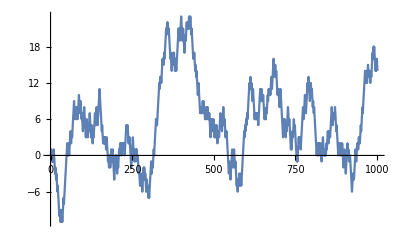

```mathematica
ListLinePlot[rwList]
```

Exercise: Define the function that has input n and N, output the list of final positions of N simulations of random walks (each after n steps). Then call the function and plot the histogram of list generated by the function.

#### Example 2 : Newton’s Method in one line

```mathematica
?NestWhileList
```

```mathematica
Clear[f]
f[x_]:=x^2-2
```

```mathematica
NestList[#-f[#]/f'[#]&,2,10]
```

```mathematica
NestWhileList[#-f[#]/f'[#]&,2,Abs[f[#]]>10^-8&]
```

{2,3/2,17/12,577/408,665857/470832}